```mathematica
Needs["QMB`"]
```

```mathematica
Import["/home/jadeleon/Documents/chaos_meets_channels/Mathematica_packages/Chaometer.wl"]
```

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
?Chaometer`*
```

```mathematica
?ChoiMatrix
```

```mathematica
L=8;
U=RandomVariate[CircularOrthogonalMatrixDistribution[2^L]];
```

```mathematica
ϕ2=RandomChainProductState[L-2];
```

```mathematica
samples=10;
Differences@MinMax@Table[
ψE=Catenate[KroneckerProduct[ϕ2,RandomQubitState[]]];
A=KroneckerProduct[IdentityMatrix[2^(L-1)],Dyad[ψE]];
Chop@Purity[ChoiMatrix[U,A,L]/2],
samples]
```

{0.00756218}

```mathematica
Differences@MinMax@Table[
ψE=Catenate[KroneckerProduct[RandomQubitState[],ϕ2]];
A=KroneckerProduct[IdentityMatrix[2^(L-1)],Dyad[ψE]];
Chop@Purity[ChoiMatrix[U,A,L]/2],
samples]
```

{0.00617092}

```mathematica
(8)(1/2.^8)
```

0.03125

```mathematica
Table[Exp[-2(0.01)^2/((L-1)(1/2.^(L-1)))],{L,20,25}]
```

{0.00401057,0.0000279314,2.11783×10^-9,2.75636×10^-17,2.09239×10^-32,1.91087×10^-61}

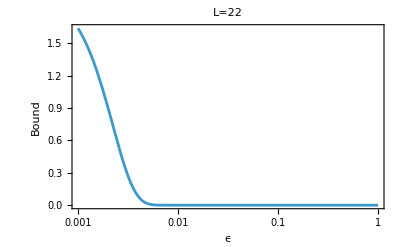

```mathematica
L=22;
LogLinearPlot[2*Exp[-2ϵ^2/((L-1)(1/2.^(L-1)))],{ϵ,0.001,1},PlotRange->All,Frame->True,FrameStyle->Directive[Black,FontSize->20],FrameTicks->{{Automatic,Automatic},{Table[{10^n,Superscript[10,n]},{n,-4,2}],Automatic}},FrameLabel->{"ϵ", "Bound"},PlotLabel->"L=22",ImageSize->400]
```